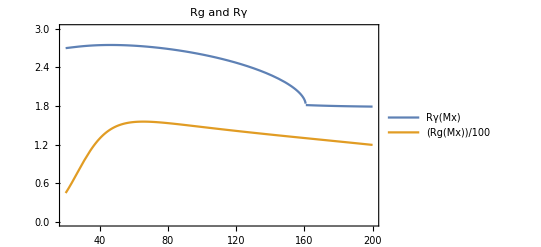

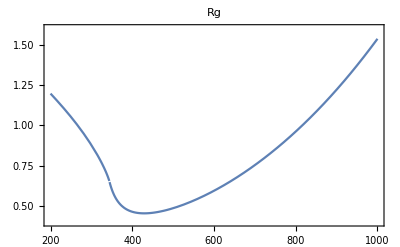

-Graphics3D-

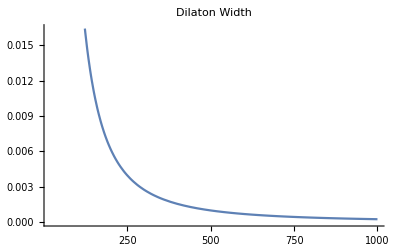

-Graphics3D-

-Graphics3D-

-Graphics3D-

0.770044

8.25918

0.157234

```mathematica
Me=.0000511;
Mμ=.1057;
Mτ=1.777;
MW=80.4;
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.4;
Mt = 172;
Mb  = 4.2;
σppH= 17.62;
σggH=1.529*10;
σVBFH=1.24;
v=246;
HiggsγγWidth=9.307*10^-6;
HiggsggWidth=3.3538*10^-4;
HiggsTotalWidth = 4.1*10^-3;
Bem[Mx_]=-11/3;
Bg[Mx_]=7;
taue[Mx_]=4*(Me^2)/(Mx^2);
tauμ[Mx_]=4*(Mμ^2)/(Mx^2);
tauτ[Mx_]=4*(Mτ^2)/(Mx^2);
tauW[Mx_]=4*(MW^2)/(Mx^2);
tauu[Mx_]=4*(Mu^2/(Mx)^2);
taud[Mx_]=4*(Md^2/(Mx)^2);
taus[Mx_]=4*(Ms^2/(Mx)^2);
tauc[Mx_]=4*(Mc^2/(Mx)^2);
taut[Mx_]=4*(Mt^2/(Mx)^2);
taub[Mx_] = 4*(Mb^2/(Mx)^2);
ft[taui_]=Piecewise[{{(ArcSin[Sqrt[1/taui]])^2,taui≥1},{(-1/4)*(Log[(1+Sqrt[1-taui])/(1-Sqrt[1-taui])]-ⅈ*π)^2,taui<1}}];
F1[tau1_]=2+3*tau1+(3*tau1)*(2-tau1)*ft[tau1];
F12[tau12_]= -2*tau12*(1+(1-tau12)*ft[tau12]);
SumLoopCorrectionRγ[Mx_]=       F12[taue[Mx]]+F12[tauμ[Mx]]+F12[tauτ[Mx]]+F1[tauW[Mx]] + 3*(2/3)^2*F12[tauu[Mx]]+3*(-1/3)^2*F12[taud[Mx]]+ 3*(2/3)^2*F12[tauc[Mx]]+3*(-1/3)^2*F12[taus[Mx]]+ 3*(2/3)^2*F12[taut[Mx]]+3*(-1/3)^2*F12[taub[Mx]];
SumLoopCorrectionRg[Mx_]=F12[tauu[Mx]]+F12[taud[Mx]]+F12[taus[Mx]]+F12[tauc[Mx]]+F12[taut[Mx]]+F12[taub[Mx]];
Rg[Mx_]=(Abs[-Bg[Mx]+(1/2)*SumLoopCorrectionRg[Mx]])^2/(Abs[(1/2)*SumLoopCorrectionRg[Mx]])^2;
Rγ[Mx_]=(Abs[-Bem[Mx]+SumLoopCorrectionRγ[Mx]])^2/(Abs[SumLoopCorrectionRγ[Mx]])^2;
σppX[f_,Mx_]=((v^2/f^2)*(Rg[Mx]*σggH+σVBFH)/(σggH+σVBFH))*σppH;
Plot[{Rγ[Mx],Rg[Mx]/100},{Mx,20,200},PlotRange ->{{20,200},{0,3}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel->"Rg and Rγ"]
Plot[Rg[Mx]/100,{Mx,200,1000},PlotRange ->{{200,1000},{.4,1.6}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel ->"Rg"]
Plot3D[σppX[f,Mx],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Production Cross Section of Dilaton",AxesLabel->{"f","Mx","Production Cross Section"}]
DilatonWidth[f_]=(v^2/f^2)* HiggsTotalWidth;
Plot[DilatonWidth[f],{f,20,1000},PlotLabel->"Dilaton Width"]
DilatonγγDecayWidth[f_,Mx_]=Rγ[Mx]*(v^2/f^2)* HiggsγγWidth;
Plot3D[DilatonγγDecayWidth[f,Mx],{f,500,3000},{Mx,0,1000},ColorFunction->"TemperatureMap",PlotLabel-> "DilatonγγDecayWidth",AxesLabel->{"f","Mx","DilatonγγDecayWidth"}]
DilatonggDecayWidth[f_,Mx_]=Rg[Mx]*(v^2/f^2)* HiggsggWidth;
Plot3D[DilatonggDecayWidth[f,Mx],{f,500,3000},{Mx,0,1000},ColorFunction->"TemperatureMap",PlotLabel-> "DilatonggDecayWidth",AxesLabel->{"f","Mx","DilatonγγDecayWidth"}]
CrossSectionRatioPPtoHiggstoGammaGamma[f_,Mx_]=(σppH*HiggsγγWidth)/(σppX[f,Mx]*DilatonγγDecayWidth[f,Mx]);
Plot3D[CrossSectionRatioPPtoHiggstoGammaGamma[f,Mx],{f,500,3000},{Mx,0,1000},ColorFunction->"TemperatureMap",PlotLabel-> "CrossSectionRatioPPtoHiggstoGammaGamma",AxesLabel->{"f","Mx","Ratio"}]
C1000f100Mx = CrossSectionRatioPPtoHiggstoGammaGamma[1000,100]
σppXC = σppX[1000,100]/σppH
γXγγC=DilatonγγDecayWidth[1000,100]/HiggsγγWidth
```